## Preliminaries

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Jaroslav Kysela\Dropbox\stimulSPDC

```mathematica
(*<<stimulSPDCpackageAbortB.wl*)
<<melvinMoreDOF2.wl
```

## Routines

Visualize setup

### Prototypes

```mathematica
prototypes=<|beamsplitter->{"path1","path2","reflang"},phaseshift->{"path1","phase"},spdcColl->{"order","path1","g","normalize"},spdcNonColl->{"order","path1","path2","g","normalize"}|>;
```

```mathematica
headLabels=<|beamsplitterOperOper->"beamsplitter",phaseshiftOperOper->"phaseshift",spdcCollOperOper->"spdcColl",spdcNonCollOperOper->"spdcNonColl"|>;
```

```mathematica
getPrototype::usage="Basically parses the Function expression corresponding to a given action. If phaseshift[#,1,phi]& is supplied to getPrototype, it returns {phaseshift,1,None,<|'head'→phaseshift,'phase'→phi|>}";
getPrototype[action_Function]:=
Module[{aux,head,path1,path2,pars,proto,path1pos,path2pos,parspos,parsnames,parsvalues},
aux=Hold[action];
head=aux[[1,1,0]];
proto=prototypes[head];

path1pos=FirstPosition[proto,"path1"|"path"];
path1=aux[[1,1,1+First@path1pos]];

path2pos=FirstPosition[proto,"path2"];
path2=If[MissingQ[path2pos],
None,
aux[[1,1,1+First@path2pos]]];

parspos=Flatten@Position[proto,Except[List|"path"|"path1"|"path2"],1];
parsnames=proto[[parspos]];
parsvalues=aux[[1,1,1+#]]&/@parspos;
pars=AssociationThread[parsnames->parsvalues];
pars=PrependTo[pars,"head"->head];
{head,path1,path2,pars}
]
```

### Add layers

```mathematica
ClearAll[addLayer]
addLayer::usage="The graph of the experimental setup is built layer by layer. To add a new layer, addLayer is used.
addLayer[action_,vertices_,edges_,dependencies_,lastind_]: 'action' is a prototype returned by getPrototype, 'vertices' is a list of vertices with labels, 'edges' is a list of Rules specifying edges, 'dependencies' is an association where keys are input path indices and values are indices of nodes where those paths currently end, 'lastind' is the index of the element added in the previous run of addLayer.";
addLayer[{vertices_,edges_,dependencies_,lastind_},action_]:=addLayer[action,vertices,edges,dependencies,lastind]
addLayer[action_,vertices_,edges_,dependencies_,lastind_]:=Module[{edge,label,head,headlabel,path1,path2,pars,newvert=vertices,newedges=edges,newdep=dependencies,newindex=lastind+1},
(*new action to add*)
{head,path1,path2,pars}=action;
headlabel=headLabels[head];
head=If[MissingQ[headlabel],head,headlabel];
edge=newdep[path1]->newindex;
newdep[path1]=newindex;
AppendTo[newedges,edge];

If[path2=!=None,
edge=newdep[path2]->newindex;
newdep[path2]=newindex;
AppendTo[newedges,edge];
];

label=Grid[KeyValueMap[List,pars],Frame->All];
AppendTo[newvert,Labeled[Tooltip[newindex,label],head]];

{newvert,newedges,newdep,newindex}
]
```

### Create graph

```mathematica
createGraphFromPrototypes::usage="Create the graph of the experimental setup. Input paths are marked with green color, output paths with red color. If coincidences are measured, corresponding output nodes are marked with black color.";
createGraphFromPrototypes[prototypes_,coincidenceList_List:{}]:=Module[{paths,inputpaths,outputpaths,dependencies,lastind,structure,lastindicesfree,lastindicescoinc,lastindicesassoc,size=.2},
(*input paths*)
paths=DeleteCases[Union[Flatten@prototypes[[All,{2,3}]]],None];
inputpaths=Labeled[Tooltip[#,Grid[{{"input",#}},Frame->All]],"Input path "<>ToString[#]]&/@paths;
outputpaths={"Output path "<>ToString[#],#,None,<|"output"->#|>}&/@paths;
dependencies=AssociationThread[paths->paths];
lastind=Max[paths];

(*create the graph structure*)
structure=Fold[addLayer,{inputpaths,{},dependencies,lastind},prototypes];
structure=Fold[addLayer,structure,outputpaths];

(*output paths*)
lastindicesassoc=structure[[-2]];
lastindicescoinc=DeleteMissing@Values[lastindicesassoc[[Key/@coincidenceList]]];
lastindicesfree=Complement[Values[lastindicesassoc],lastindicescoinc];

(*create visual representation of the graph*)
Graph[Sequence@@structure[[;;2]],
GraphLayout->{"LayeredDigraphEmbedding", "Orientation"->Left},
ImageSize->Large,
VertexStyle->Join[Thread[paths->Green],Thread[lastindicesfree->Red],Thread[lastindicescoinc->Black]],
VertexSize->Join[Thread[paths->size],Thread[lastindicesfree->size],Thread[lastindicescoinc->size]]
]
]
```

```mathematica
visualizeSetup[setup_,coincidenceList_List:{}]:=Module[{},
createGraphFromPrototypes[getPrototype/@setup,coincidenceList]
]
```

### Tests

```mathematica
ss={spdcNonColl[#1,2,2,3,g,False]&,phaseshift[#1,1,π/3]&,spdcColl[#1,2,1,g,False]&,phaseshift[#1,1,π]&,phaseshift[#1,2,π/3]&,phaseshift[#1,1,π/2]&,phaseshift[#1,3,π/2]&,spdcNonColl[#1,2,1,2,g,False]&,phaseshift[#1,2,π]&,phaseshift[#1,1,(2 π)/3]&};
```

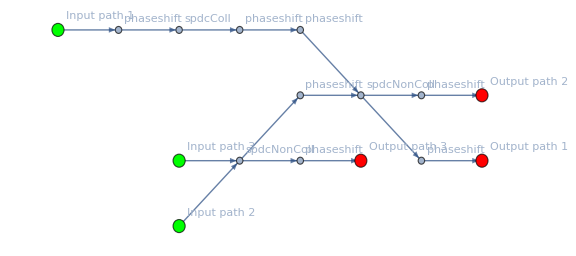

```mathematica
visualizeSetup[ss]
```

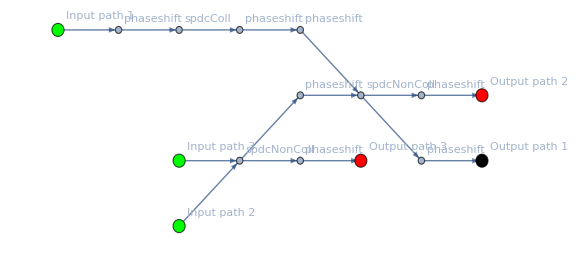

```mathematica
visualizeSetup[ss,{1,100}]
```

Analysis

```mathematica
ClearAll[analyzeSetup]
```

```mathematica
analyzeSetup[filename_String]:=Module[{data,coincList},
data=Get[filename];
(*Print[data["matches"]];*)
coincList=data["coincidenceList"];
If[MissingQ@coincList,coincList={}];
analyzeSetup[data["setup"],data["initState"],data["referencePatterns"],coincList,data["couplingConstant"],data["outputState"],data["unwantedPatternsZero"],data["unwantedPatternsFirst"],filename]
]
```

```mathematica
analyzeSetup[setup_,inputState_,referencePatterns_,coincidenceList_:{},couplconst_:g,outputStateIn_:None,unwantedPatternsZero_:None,unwantedPatternsFirst_:None,filename_:None]:=Module[{outputState,zeroOrder,firstOrder,coef,coefconj,visu,precompl,postcompl,assoc,matches,nonmatches,grid,initState=inputState,nm0,nm1,nm1c},
(*visualization of the setup*)
visu=visualizeSetup[setup,coincidenceList];

If[outputStateIn=!=None,
(*if output state is also supplied do not calculate it again*)
outputState=outputStateIn
,
(*generate state and estimate complexity before and after simplification*)
outputState=(Composition@@setup)[initState];

If[Length@coincidenceList>0,outputState=coincidenceDetection[outputState,coincidenceList,True];];

precompl=Count[outputState,$pattern,Infinity];
outputState=Collect[outputState,$pattern,Simplify];
postcompl=Count[outputState,$pattern,Infinity];
];

zeroOrder=getGCoeff[outputState,couplconst,0];
firstOrder=getGCoeff[outputState,couplconst,1];
{coef,coefconj}={Coefficient[firstOrder,couplconst],Coefficient[firstOrder,couplconst*]};

matches=relevantTerms[firstOrder,referencePatterns,True];
(*nm0=Cases[zeroOrder,unwantedPatternsZero];
nm1=Cases[coef,unwantedPatternsFirst];
nm1c=Cases[coefconj,unwantedPatternsFirst];
nonmatches=Plus@@nm0+couplconst Plus@@nm1+couplconst* Plus@@nm1c;*)
(*nonmatches=Cases[firstOrder,unwantedPatternsFirst];*)
nonmatches=relevantTerms[firstOrder,unwantedPatternsFirst,True];
grid={
{"file name",filename},{"visualization",visu},
{"terms satisfying criteria",Item[matches,Background->LightGreen]},
{"unwanted parts in 1st order",Item[nonmatches,Background->LightOrange]},
{"state complexity estimate",Count[outputState,$pattern,Infinity]},
{"coincidences triggering paths",coincidenceList},
{"input state",initState},
{"reference patterns",referencePatterns},
{"highlighted first order",Block[{$pattern=_Ket},highlightTerms[operToKet@firstOrder]]},
{"zero order",Block[{$pattern=_Ket},highlightTerms[operToKet@zeroOrder]]},
{"unwanted patterns in 1st order",unwantedPatternsFirst}
(*{"output state",Shallow[outputState]},*)(*,{"first order g",coef},{"first order g*",coefconj}*)
};

Grid[grid,Alignment->{{Right,Left},Center},Background->{{LightGray},None},Frame->All]
]
```

## Analysis

Set Directory

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Jaroslav Kysela\Dropbox\stimulSPDC

```mathematica
(*SetDirectory["C:\\Users\\Jaroslav Kysela\\Desktop\\stimulSPDC"]*)
```

```mathematica
dir=;
SetDirectory[dir]
```

C:\Users\Jaroslav Kysela\Dropbox\stimulSPDC\setups_Thu_07_3_2019

```mathematica
files=FileNames[];
Length[files]
```

3

Set file

```mathematica
file=;
(*file=files[[1]]*)
```

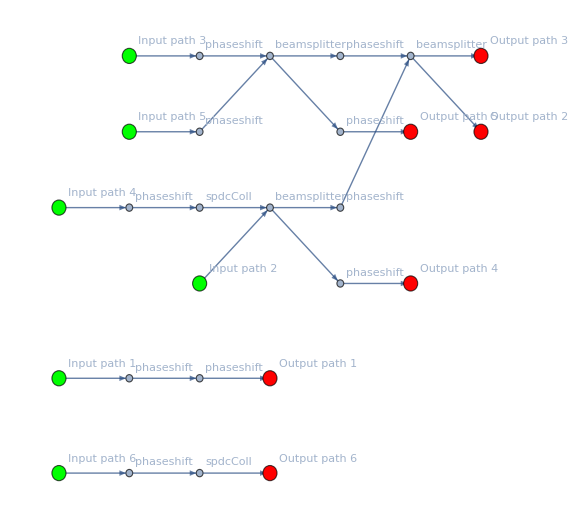
file name | C:\Users\Jaroslav Kysela\Dropbox\stimulSPDC\setups_Fri_08_3_2019\setup_Fri_08_3_2019_13h41m26s.txt
visualization | -Graphics-
terms satisfying criteria | {{{((-1)^(5/6) g β ad[2] ad[3] ad[6]^2)/(2 √2)},{-1/2 (-1)^(1/3) g α ad[2] ad[4] ad[6]^2}}}
unwanted parts in 1st order | {{{}},{{}},{{}},{{}}}
state complexity estimate | 119
coincidences triggering paths | {}
input state | α ad[2] ad[3]+β ad[2] ad[4]
reference patterns | {{β ad[2] ad[3] _?(FreeQ[ad[1]|ad[4]]),α ad[2] ad[4] _?(FreeQ[ad[1]|ad[3]])}}
highlighted first order | 0,0,0,0,0,0 1/2 ⅈ (α-√2 β) Conjugate[g]+0,0,0,2,0,2 1/2 (-1)^(5/6) g (α-√2 β)+0,0,0,4,0,0 ⅈ √(3/2) g (√2 β-α)+0,2,0,0,0,2 -1/2 (-1)^(5/6) g (α+√2 β)+0,2,0,2,0,0 1/2 ⅈ g (α+√2 β)+-1/2 ⅈ α g 0,0,0,0,2,2+1/2 -1^(1/6) α g 0,0,0,2,2,0+-(-1^(1/6) α g)/(√2) 0,0,1,0,1,2+-((-1)^(5/6) α g)/(√2) 0,0,1,2,1,0+1/2 (-1)^(5/6) α g 0,0,2,0,0,2+-1/2 ⅈ α g 0,0,2,2,0,0+-(-1^(1/3) α g)/(√2) 0,1,0,1,0,2+√(3/2) α g 0,1,0,3,0,0+-1/2 (-1)^(2/3) β g 0,0,0,1,1,2+1/2 -1^(1/3) √3 β g 0,0,0,3,1,0+-1/2 -1^(1/3) β g 0,0,1,1,0,2+1/2 √3 β g 0,0,1,3,0,0+-1/2 -1^(1/6) β g 0,1,0,0,1,2+-1/2 (-1)^(5/6) β g 0,1,0,2,1,0+1/2 (-1)^(5/6) β g 0,1,1,0,0,2+-1/2 ⅈ β g 0,1,1,2,0,0
zero order | -1/4 ⅈ (√2 α-2 β) 0,0,0,2,0,0+(ⅈ (α+√2 β))/(2 √2) 0,2,0,0,0,0+(-1^(1/6) α)/(2 √2) 0,0,0,0,2,0+-1/2 (-1)^(5/6) α 0,0,1,0,1,0+-(ⅈ α)/(2 √2) 0,0,2,0,0,0+α/2 0,1,0,1,0,0+(-1^(1/3) β)/(2 √2) 0,0,0,1,1,0+β/(2 √2) 0,0,1,1,0,0+-((-1)^(5/6) β)/(2 √2) 0,1,0,0,1,0+-(ⅈ β)/(2 √2) 0,1,1,0,0,0
unwanted patterns in 1st order | {{__ _?Positive,0,0,0,___},{__ 0,_?Positive,0,0,___},{__ 0,0,_?Positive,0,___},{__ 0,0,0,_?Positive,___}}

```mathematica
analyzeSetup[file(*files[[-1]]*)]
```